### Eigenvalues of the band matrix

```mathematica
Eigenvalues[{{1,1,0},{1,0,1},{0,1,1}}]
Eigenvalues[{{1,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1}}]
Eigenvalues[{{1,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,1}}]
Eigenvalues[{{1,1,0,0,0,0},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{0,0,0,0,1,1}}]
Eigenvalues[{{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{0,1,0,1,0,0,0},{0,0,1,0,1,0,0},{0,0,0,1,0,1,0},
{0,0,0,0,1,0,1},{0,0,0,0,0,1,1}}]
Eigenvalues[{{1,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0},
{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,1}}]
Eigenvalues[{{1,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0},
{0,0,0,0,1,0,1,0,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,1,1}}]
Eigenvalues[{{1,1,0,0,0,0,0,0,0,0},
{1,0,1,0,0,0,0,0,0,0},
{0,1,0,1,0,0,0,0,0,0},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,0},
{0,0,0,0,1,0,1,0,0,0},
{0,0,0,0,0,1,0,1,0,0},
{0,0,0,0,0,0,1,0,1,0},
{0,0,0,0,0,0,0,1,0,1},
{0,0,0,0,0,0,0,0,1,1}}]
N[%]
```

{2,-1,1}

{2,-√2,√2,0}

{2,1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

{2,-√3,√3,-1,1,0}

{2,Root[-1-2 #1+#1^2+#1^3&,1],Root[1-2 #1-#1^2+#1^3&,3],Root[1-2 #1-#1^2+#1^3&,1],Root[-1-2 #1+#1^2+#1^3&,3],Root[-1-2 #1+#1^2+#1^3&,2],Root[1-2 #1-#1^2+#1^3&,2]}

{-2-√(2+√2),-2-√2,-2-√(2-√2),-2,-2+√(2-√2),-2+√2,-2+√(2+√2),0}

{Root[3+9 #1+6 #1^2+#1^3&,1],Root[1+9 #1+6 #1^2+#1^3&,1],-3,Root[1+9 #1+6 #1^2+#1^3&,2],Root[3+9 #1+6 #1^2+#1^3&,2],-1,Root[3+9 #1+6 #1^2+#1^3&,3],Root[1+9 #1+6 #1^2+#1^3&,3],0}

{2,-√(1/2 (5+√5)),√(1/2 (5+√5)),1/2 (-1-√5),1/2 (1+√5),-√(1/2 (5-√5)),√(1/2 (5-√5)),1/2 (1-√5),1/2 (-1+√5),0}

{2.,-1.90211,1.90211,-1.61803,1.61803,-1.17557,1.17557,-0.618034,0.618034,0.}

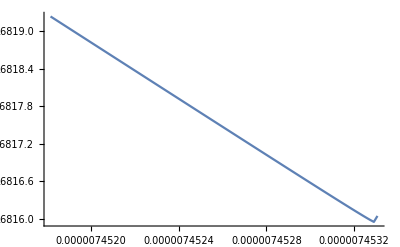

```mathematica
pm=5;
f[x_]:=NIntegrate[Exp[-p^2]/(2Exp[-p^2/2]-x),{p,0,pm}]/(x pm);
Plot[f[x],{x,(2-0.01/pm^2) Exp[-pm^2/2],2Exp[-pm^2/2]}]
```

### Minimization of the error function for nearest neighbor updates

#### Perfect sampling

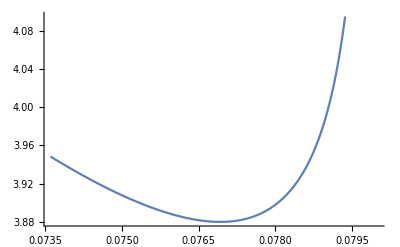

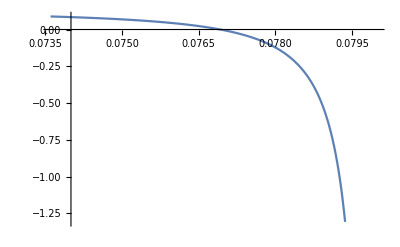

```mathematica
m1=0.24;
(* error function *)
f1[x_]:=NIntegrate[(1-4m1 Cos[p]^2)^2/(2-8m1 Cos[p]^2-x),{p,0,Pi/2}]2/Pi/x;
Plot[f1[x],{x,2-8m1-4(1-4m1)^2,2-8m1}]

(* derivative of the error function *)
g1[x_]:=NIntegrate[(1-4m1 Cos[p]^2-x)/(2-x/(1-4m1 Cos[p]^2))^2,{p,0,Pi/2}]2/Pi;
Plot[g1[x],{x,2-8m1-4(1-4m1)^2,2-8m1}]
```

```mathematica
Integrate[(2/Pi)(1-4 m1 Cos[p]^2)^2/(2-8 m1 Cos[p]^2-b),{p,0,Pi/2},Assumptions->{4m1<1&&4m1>0&&b>0&&b<2-8m1}]
```

1/4 (2+b-4 m1+b^2/(√((-2+b) (-2+b+8 m1))))

```mathematica
ff=(z^2-m1(z^2+1)^2)^2/((2-y)z^2-2m1(z^2+1)^2)/z^2;
Series[ff,{z,0,5}]
num =Numerator[ff];
den =D[Denominator[ff]/z^2,z];
num/den
gg=FullSimplify[num/den/z^3/y]
FullSimplify[gg/.{z->(Sqrt[2-y]-Sqrt[2-y-8m1])/Sqrt[8m1]}]
```

-m1/(2 z^2)+1/4 (2-4 m1+y)+(-m1/2-y^2/(8 m1)) z^2+((-2 y^2+4 m1 y^2+y^3) z^4)/(16 m1^2)+O[z]^6

((z^2-m1 (1+z^2)^2)^2)/(2 (2-y) z-8 m1 z (1+z^2))

-((z^2-m1 (1+z^2)^2)^2)/(2 y z^4 (-2+y+4 m1 (1+z^2)))

y/(8 √(2-y) √(2-8 m1-y))

```mathematica
{(1-2m1)/(1-4m1),1+2 m1^2/(1-4m1)}/.{m1->0.24}
```

{13.,3.88}

#### One-step sampling

```mathematica
Integrate[(2/Pi)(1-4 m1 Cos[p]^2)^2/(2-8 m1 Cos[p]^2-b)Sin[p]^2/(Cos[p]^2 +d^2),{p,0,Pi/2},Assumptions->{4m1<1/2&&m1>0&&b>0&&b<2-8m1&&d<1/100&&d>0}]
Apart[%]
```

-(-4 √(1+d^2)+d (4+8 m1-4 b m1+b^2 (-1+√(1+(8 m1)/(-2+b)))+32 d m1 (-√(1+d^2)+d (1+m1+2 d^2 m1-2 d √(1+d^2) m1))))/(4 d (2-b+8 d^2 m1))

(√(1+d^2))/((2-b) d)+1/4 (-2-b-4 m1)-2 d^2 m1+2 d √(1+d^2) m1+(2 b^2 d √(1+d^2) m1)/((-2+b) (2-b+8 d^2 m1))-(b^2 √((-2+b+8 m1)/(-2+b)))/(4 (2-b+8 d^2 m1))

```mathematica
FullSimplify[(√(1+d^2))/((2-b) d)+2 d √(1+d^2) m1+(2 b^2 d √(1+d^2) m1)/((-2+b) (2-b+8 d^2 m1))]
```

(√(1+d^2) (1+4 d^2 m1)^2)/(d (2-b+8 d^2 m1))

### Exact schedule

```mathematica
aval=1;
bval=1/2;
DSolve[{a^2Exp[2a q[t]](q''[t]+q'[t]^2a)+b^2Exp[2b q[t]](q''[t]+q'[t]^2b)==0}/.{a->aval, b->bval},q[t],t]
```

{{q[t]→InverseFunction[(ⅇ^(#1/2) √(1+4 ⅇ^#1)+1/2 ArcSinh[2 ⅇ^(#1/2)])/C[1]&][t+C[2]]}}

```mathematica
aval=1;
bval=1/2;
DSolve[{F a^2Exp[2a q[t]](q''[t]+q'[t]^2a)+G b^2Exp[2b q[t]](q''[t]+q'[t]^2b)==0}/.{a->aval, b->bval},q[t],t]
```

{{q[t]→InverseFunction[(ⅇ^(#1/2) √(4 ⅇ^#1 F+G)+(G Log[2 ⅇ^(#1/2) F+√F √(4 ⅇ^#1 F+G)])/(2 √F))/C[1]&][t+C[2]]}}

```mathematica
DSolve[{F a^2Exp[2a q[t]](q''[t]+q'[t]^2a)+G b^2Exp[2b q[t]](q''[t]+q'[t]^2b)==0},q[t],t]
```

{{q[t]→InverseFunction[((2 a-b) (a^2 ⅇ^(2 a #1) F+b^2 ⅇ^(2 b #1) G)+a^2 (-a+b) ⅇ^(2 a #1) F √(1+(a^2 ⅇ^(2 (a-b) #1) F)/(b^2 G)) Hypergeometric2F1[1/2,(2 a-b)/(2 a-2 b),(4 a-3 b)/(2 a-2 b),-(a^2 ⅇ^(2 (a-b) #1) F)/(b^2 G)])/((2 a-b) b √(a^2 ⅇ^(2 a #1) F+b^2 ⅇ^(2 b #1) G) C[1])&][t+C[2]]}}

```mathematica
DSolve[{F a^2Exp[2a q[t]](q''[t]+q'[t]^2a)+G b^2Exp[2b q[t]](q''[t]+q'[t]^2b)+L c^2Exp[2c q[t]](q''[t]+q'[t]^2c)==0},q[t],t]
```

{{q[t]→InverseFunction[∫_1^#1 (√(a^2 ⅇ^(2 a K[1]) F+b^2 ⅇ^(2 b K[1]) G+c^2 ⅇ^(2 c K[1]) L))/C[1]ⅆK[1]&][t+C[2]]}}

### Fourier transform of an optimal scheme

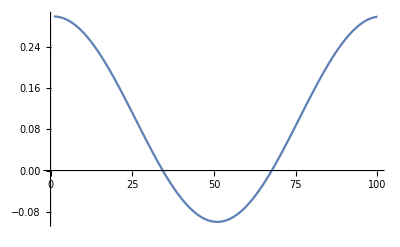

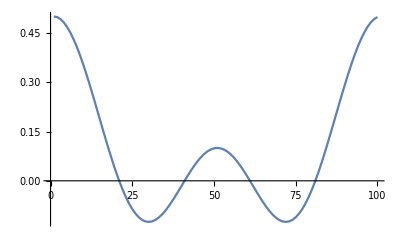

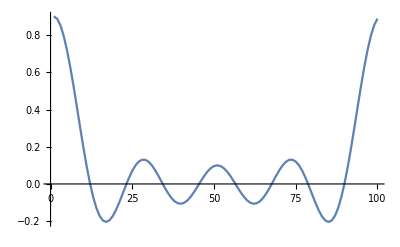

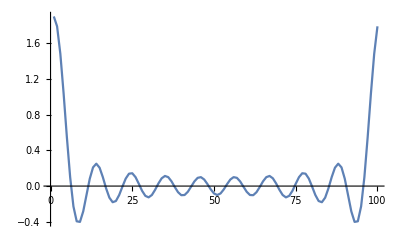

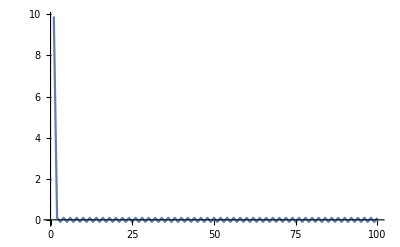

```mathematica
mkstep[n_,kmax_]:=Table[If[i≤kmax||i>n+1-kmax,1,0],{i,n}];
ListPlot[Re[Fourier[mkstep[100,2]]],Joined->True,PlotRange->All]
ListPlot[Re[Fourier[mkstep[100,3]]],Joined->True,PlotRange->All]
ListPlot[Re[Fourier[mkstep[100,5]]],Joined->True,PlotRange->All]
ListPlot[Re[Fourier[mkstep[100,10]]],Joined->True,PlotRange->All]
ListPlot[Re[Fourier[mkstep[100,50]]],Joined->True,PlotRange->All]
```

### Sums of the optimal updating scheme

{3/4,1/4,-1/4,1/4}

{5/3,-1/3,-1/3}

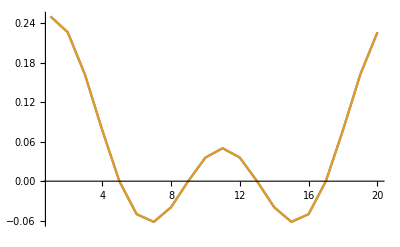

1

```mathematica
mupbc[n_,l_,km_]:=If[l==0,(2km+1)/n,Sin[(2km+1)l Pi/n]/Sin[l Pi/n]/n];
Table[FullSimplify[mupbc[4,l,1]],{l,0,3}]
Table[FullSimplify[mupbc[3,l,2]],{l,0,2}]
mksteppbc[n_,kmax_]:=Table[If[i≤kmax||i>n+1-kmax,1,0],{i,n}];
ListPlot[
{Table[mupbc[20,l,2],{l,0,19}],
Fourier[mksteppbc[20,3]]/Sqrt[20]},
Joined->True,PlotRange->All]
musumpbc[n_,km_]:=FullSimplify[Sum[mupbc[n,l,km],{l,0,n-1}]];
musumpbc[20,1]
```

{1/3,1/2,-1/6}

{1/2,1/8 (-1+Cot[π/8]),1/4,1/8 (-1-Tan[π/8])}

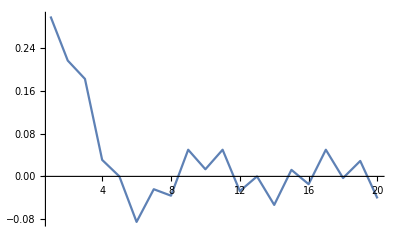

1

```mathematica
munonpbc[n_,l_,km_]:=((-1)^(n+km+l-1)+If[l==0,(2km+1),Sin[(2km+1)l Pi/(2n)]/Sin[l Pi/(2n)]])/(2n);
Table[FullSimplify[munonpbc[3,l,1]],{l,0,2}]
Table[FullSimplify[munonpbc[4,l,1]],{l,0,3}]
ListPlot[Table[N[munonpbc[20,l,5]],{l,0,19}],Joined->True,PlotRange->All]
musumnonpbc[n_,km_]:=FullSimplify[2Sum[munonpbc[n,l,km],{l,1,n-1}]+munonpbc[n,0,km]];
musumnonpbc[12,1]
```

```mathematica
Table[FullSimplify[munonpbc[3,l,1]],{l,0,2}]
```

{1/3,1/2,-1/6}